## Process metadata

This process allows for some cleanup of the metadata gathered and re-exported into cleaner, easier to use EntityStores for exploration.

### Load Paclet

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
Get["CodeGolfSEAnalysis`"]
```

### Load prefetched EntityStores

These were generated in GatherMetadata.nb:

```mathematica
SetDirectory[NotebookDirectory[]];
codeGolfEntityStore=Import["codegolf.stackexchange.com_WithMetadata_2019-10-21_22-53-37.mx"];
EntityUnregister/@codeGolfEntityStore[];
EntityRegister[codeGolfEntityStore]

SetDirectory[NotebookDirectory[]];
codeGolfLanguageEntityStore=Import["CodeGolfProgrammingLanguage_2019-10-21_22-54-18.mx"];
EntityUnregister/@codeGolfLanguageEntityStore[];
EntityRegister[codeGolfLanguageEntityStore]
```

{StackExchange.Codegolf:User,StackExchange.Codegolf:Badge,StackExchange.Codegolf:Comment,StackExchange.Codegolf:Post,StackExchange:PostType,StackExchange.Codegolf:Vote,StackExchange:VoteType,StackExchange.Codegolf:PostHistory,StackExchange:PostHistoryType,StackExchange:CloseReason,StackExchange.Codegolf:Tag}

{CodeGolfProgrammingLanguage}

### Merge/Clean up programming language EntityStore

#### List of languages that can be merged

I manually sifted through the top several hundred and searched for possible duplicates.
Some of these are arbitrary, some are limitations to the name processing code.

```mathematica
languageToAlternatives=<|Entity["CodeGolfProgrammingLanguage","JavaScript::g3427"]->{Entity["CodeGolfProgrammingLanguage","javascriptes"],Entity["CodeGolfProgrammingLanguage","node.js"],Entity["CodeGolfProgrammingLanguage","nodejs"],Entity["CodeGolfProgrammingLanguage","node"],Entity["CodeGolfProgrammingLanguage","jses"],Entity["CodeGolfProgrammingLanguage","javascript/es"],Entity["CodeGolfProgrammingLanguage","js"]},
Entity["CodeGolfProgrammingLanguage","APL::nh588"]->{Entity["CodeGolfProgrammingLanguage","dyalogapl"],Entity["CodeGolfProgrammingLanguage","apl(dyalog"],Entity["CodeGolfProgrammingLanguage","dyalogaplextended"],Entity["CodeGolfProgrammingLanguage","apl(nars"],Entity["CodeGolfProgrammingLanguage","apl𝒿win"],Entity["CodeGolfProgrammingLanguage","aplnars"],Entity["CodeGolfProgrammingLanguage","apl𝒿score"],Entity["CodeGolfProgrammingLanguage","apl(dyalogclassic"],Entity["CodeGolfProgrammingLanguage","apl𝒿mauris"],Entity["CodeGolfProgrammingLanguage","apl𝒿size"]},
Entity["CodeGolfProgrammingLanguage","powershell"]->{Entity["CodeGolfProgrammingLanguage","WindowsPowerShell::886h5"],Entity["CodeGolfProgrammingLanguage","powershellcore"],Entity["CodeGolfProgrammingLanguage","powershell𝒿score"],Entity["CodeGolfProgrammingLanguage","powershell𝒿≤"],Entity["CodeGolfProgrammingLanguage","powershellforwindows"]},
Entity["CodeGolfProgrammingLanguage","WolframLanguage"]->{Entity["CodeGolfProgrammingLanguage","wolframmathematica"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿score"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿wolfram"],Entity["CodeGolfProgrammingLanguage","wolframmethematica"],Entity["CodeGolfProgrammingLanguage","wolfram≅"],Entity["CodeGolfProgrammingLanguage","mathematicasimplified"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿@martinender"],Entity["CodeGolfProgrammingLanguage","mathematicaonwindows"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿n="],Entity["CodeGolfProgrammingLanguage","mathematica𝒿size"],Entity["CodeGolfProgrammingLanguage","mathematica𝒿l="]},
Entity["CodeGolfProgrammingLanguage","C::5zm8v"]->{Entity["CodeGolfProgrammingLanguage","csharp"],Entity["CodeGolfProgrammingLanguage","c𝒿sharp"],Entity["CodeGolfProgrammingLanguage","C::5zm8v"],Entity["CodeGolfProgrammingLanguage","c#.net"],Entity["CodeGolfProgrammingLanguage","c#inlinqpad"],Entity["CodeGolfProgrammingLanguage","c#𝒿linq"],Entity["CodeGolfProgrammingLanguage","c#𝒿linqpad"],Entity["CodeGolfProgrammingLanguage","c#wpf"],Entity["CodeGolfProgrammingLanguage","c#linq"]},
Entity["CodeGolfProgrammingLanguage","F::549k5"]->{Entity["CodeGolfProgrammingLanguage","fsharp"]},
Entity["CodeGolfProgrammingLanguage","><>"]->{Entity["CodeGolfProgrammingLanguage","><>fish"]},
Entity["CodeGolfProgrammingLanguage","C::p5vhv"]->{Entity["CodeGolfProgrammingLanguage","ANSIC::8zh69"],Entity["CodeGolfProgrammingLanguage","cpreprocessor"]},
Entity["CodeGolfProgrammingLanguage","PHP::x8873"]->{Entity["CodeGolfProgrammingLanguage","php>="]},
Entity["CodeGolfProgrammingLanguage","Brainfuck::8mj43"]->{Entity["CodeGolfProgrammingLanguage","brainf***"],Entity["CodeGolfProgrammingLanguage","brainf*ck"],Entity["CodeGolfProgrammingLanguage","self-modifyingbrainfu\[FreakedSmiley]\[FreakedSmiley]"],Entity["CodeGolfProgrammingLanguage","extendedbrainfu\[FreakedSmiley]\[FreakedSmiley]"],Entity["CodeGolfProgrammingLanguage","brainf**k"],Entity["CodeGolfProgrammingLanguage","bf"],Entity["CodeGolfProgrammingLanguage","smbf"],Entity["CodeGolfProgrammingLanguage","self-modifyingbrainf***"],Entity["CodeGolfProgrammingLanguage","self-modifyingbrainf*ck"],Entity["CodeGolfProgrammingLanguage","brainfu\[FreakedSmiley]\[FreakedSmiley]"],Entity["CodeGolfProgrammingLanguage","randombrainfu\[FreakedSmiley]\[FreakedSmiley]"]},
Entity["CodeGolfProgrammingLanguage","windowsbatch"]->{Entity["CodeGolfProgrammingLanguage","batchfile"],Entity["CodeGolfProgrammingLanguage","windowscommand"],Entity["CodeGolfProgrammingLanguage","windowsbatchfile"],Entity["CodeGolfProgrammingLanguage","windowscommandprompt"],Entity["CodeGolfProgrammingLanguage","batch"],Entity["CodeGolfProgrammingLanguage","cmd.exe"],Entity["CodeGolfProgrammingLanguage","windowscmd"],Entity["CodeGolfProgrammingLanguage","windowscommandshell"]},
Entity["CodeGolfProgrammingLanguage","Go::3m7v3"]->{Entity["CodeGolfProgrammingLanguage","golang"]},
Entity["CodeGolfProgrammingLanguage","Lua::9nnwp"]->{Entity["CodeGolfProgrammingLanguage","luaforwindows"]},
Entity["CodeGolfProgrammingLanguage","x86"]->{Entity["CodeGolfProgrammingLanguage","x86machine"],Entity["CodeGolfProgrammingLanguage","X86AssemblyLanguage::8wgc4"],Entity["CodeGolfProgrammingLanguage","x86_"],Entity["CodeGolfProgrammingLanguage","x86assembler"],Entity["CodeGolfProgrammingLanguage","x86"],Entity["CodeGolfProgrammingLanguage","x86opcode"],Entity["CodeGolfProgrammingLanguage","x8632-bitmachine"],Entity["CodeGolfProgrammingLanguage","x86machinecodeondos"],Entity["CodeGolfProgrammingLanguage","x86.com"],Entity["CodeGolfProgrammingLanguage","x86asm"],Entity["CodeGolfProgrammingLanguage","cpux86"],Entity["CodeGolfProgrammingLanguage","/32-bitx86assembly"],Entity["CodeGolfProgrammingLanguage","machinecodeonx86_"],Entity["CodeGolfProgrammingLanguage","x86andx"],Entity["CodeGolfProgrammingLanguage","x86opcode(.com"],Entity["CodeGolfProgrammingLanguage","x8616bitrealmodeassembly"],Entity["CodeGolfProgrammingLanguage","x86tasm"],Entity["CodeGolfProgrammingLanguage","x86machinecodeonms𝒿dos"],Entity["CodeGolfProgrammingLanguage","little𝒿endianx86machine"],Entity["CodeGolfProgrammingLanguage","x86ms𝒿dos.comfile"],Entity["CodeGolfProgrammingLanguage","x86machine𝒿code"]},
Entity["CodeGolfProgrammingLanguage","shakespeare"]->{Entity["CodeGolfProgrammingLanguage","shakespeareprogramming"]},
Entity["CodeGolfProgrammingLanguage","matlab/octave"]->{Entity["CodeGolfProgrammingLanguage","octave"],Entity["CodeGolfProgrammingLanguage","matlab𝒿octave"],Entity["CodeGolfProgrammingLanguage","matlab/octave"],Entity["CodeGolfProgrammingLanguage","octave𝒿matlab"],Entity["CodeGolfProgrammingLanguage","octave𝒿score"],Entity["CodeGolfProgrammingLanguage","MATLAB::82q2f"]},
Entity["CodeGolfProgrammingLanguage","Lisp::tnvy6"]->{Entity["CodeGolfProgrammingLanguage","CommonLisp::6p4h5"],Entity["CodeGolfProgrammingLanguage","EmacsLisp::5m82g"]}
|>;
languageToPreferredLanguage=languageToAlternatives//KeyValueMap[Thread[Rule[#2,#1]]&]//Flatten//DeleteDuplicates//Select[Apply[UnsameQ]]//Association;
```

```mathematica
languageToPreferredLanguage
```

<|JavaScript ES→JavaScript,Node.js→JavaScript,NodeJS→JavaScript,Node→JavaScript,JS ES→JavaScript,Javascript / ES→JavaScript,JS→JavaScript,Dyalog APL→APL,APL(Dyalog→APL,Dyalog APL Extended→APL,APL(NARS→APL,APL𝒥WIN→APL,APL NARS→APL,APL𝒥 score→APL,APL(Dyalog Classic→APL,APL𝒥 Mauris→APL,APL𝒥 size→APL,Windows PowerShell→PowerShell,PowerShell Core→PowerShell,PowerShell𝒥 score→PowerShell,Powershell𝒥 ≤→PowerShell,PowerShell for Windows→PowerShell,Wolfram Mathematica→Wolfram Language,Mathematica𝒥 score→Wolfram Language,Mathematica 𝒥 Wolfram→Wolfram Language,Wolfram Methematica→Wolfram Language,Wolfram ≅→Wolfram Language,Mathematica Simplified→Wolfram Language,Mathematica𝒥 @Martin Ender→Wolfram Language,Mathematica on Windows→Wolfram Language,Mathematica𝒥 n=→Wolfram Language,Mathematica𝒥 size→Wolfram Language,Mathematica𝒥 L=→Wolfram Language,CSharp→C#,C𝒥Sharp→C#,C# .NET→C#,C# in LINQPAD→C#,C# 𝒥 Linq→C#,C# 𝒥 LINQPad→C#,C# WPF→C#,C# LINQ→C#,FSharp→F#,><> Fish→><>,ANSI C→C,C Preprocessor→C,PHP>=→PHP,Brainf***→Brainfu\[FreakedSmiley]\[FreakedSmiley],Brainf*ck→Brainfu\[FreakedSmiley]\[FreakedSmiley],Self-modifying Brainfu\[FreakedSmiley]\[FreakedSmiley]→Brainfu\[FreakedSmiley]\[FreakedSmiley],Extended BrainFu\[FreakedSmiley]\[FreakedSmiley]→Brainfu\[FreakedSmiley]\[FreakedSmiley],Brainf**k→Brainfu\[FreakedSmiley]\[FreakedSmiley],BF→Brainfu\[FreakedSmiley]\[FreakedSmiley],SMBF→Brainfu\[FreakedSmiley]\[FreakedSmiley],Self-modifying Brainf***→Brainfu\[FreakedSmiley]\[FreakedSmiley],Self-modifying Brainf*ck→Brainfu\[FreakedSmiley]\[FreakedSmiley],Brainfu\[FreakedSmiley]\[FreakedSmiley]→Brainfu\[FreakedSmiley]\[FreakedSmiley],Random Brainfu\[FreakedSmiley]\[FreakedSmiley]→Brainfu\[FreakedSmiley]\[FreakedSmiley],Batch File→Windows batch,Windows Command→Windows batch,Windows Batch File→Windows batch,Windows Command Prompt→Windows batch,Batch→Windows batch,cmd.exe→Windows batch,Windows CMD→Windows batch,Windows command shell→Windows batch,Golang→Go,lua for windows→Lua,x86 Machine→x86,x86 assembly language→x86,x86_→x86,x86 Assembler→x86,x86 opcode→x86,x86 32-bit machine→x86,x86 machine code on DOS→x86,x86 .COM→x86,x86 asm→x86,CPU x86→x86,/32-bit x86 assembly→x86,MachineCode on x86_→x86,x86 and x→x86,x86 opcode(.COM→x86,x86 16 bit real mode Assembly→x86,x86 TASM→x86,x86 machine code on MS𝒥DOS→x86,little𝒥endian x86 machine→x86,x86 MS𝒥DOS .COM file→x86,x86 machine𝒥code→x86,Shakespeare Programming→Shakespeare,Octave→MATLAB/Octave,Matlab 𝒥 Octave→MATLAB/Octave,Octave 𝒥 MATLAB→MATLAB/Octave,Octave𝒥 score→MATLAB/Octave,MATLAB→MATLAB/Octave,Common Lisp→Lisp,Emacs Lisp→Lisp|>

#### Merge language entities in the Metadata

```mathematica
postToMetadata=EntityValue["StackExchange.Codegolf:Post","CodeGolfMetadata","EntityAssociation"];
postToMetadata//Length
```

154104

```mathematica
postToFixedMetadata=Replace[a_Association/;KeyMemberQ[a,"Language"]:>Append[a,"Language"->Lookup[languageToPreferredLanguage,a["Language"],a["Language"]]]]/@postToMetadata;
```

```mathematica
KeyValueMap[(#1["CodeGolfMetadata"]=.;#1["CodeGolfMetadata"]=#2;)&,postToFixedMetadata];//AbsoluteTiming
```

{52.4884,Null}

```mathematica
postToMetadata2=EntityValue["StackExchange.Codegolf:Post","CodeGolfMetadata","EntityAssociation"];
postToMetadata2//Length
```

154104

```mathematica
Select[postToMetadata2,#["Language"]===Entity["CodeGolfProgrammingLanguage","javascriptes"]&,1]
```

<||>

#### Merge and update language entities in the language EntityStore

```mathematica
languageToURLCounts=GroupBy[Select[Lookup[Values[postToMetadata2],{"Language","TitleURLs"}],FreeQ[_Missing]],First->Last,Flatten/*Counts/*ReverseSort]//ReverseSortBy[Total];
languageToURLCounts//Length
```

2484

```mathematica
Total/@languageToURLCounts[[;;12]]
```

<|Jelly→5175,Python→5119,05AB1E→3502,Perl→2609,APL→1884,MATL→1545,Haskell→1476,Japt→1433,Retina→1417,R→1181,C→1118,Ruby→1097|>

```mathematica
Keys/*First/@languageToURLCounts[[;;12]]
```

<|Jelly→https://github.com/DennisMitchell/jelly,Python→https://docs.python.org/2/,05AB1E→https://github.com/Adriandmen/05AB1E,Perl→https://www.perl.org/,APL→https://www.dyalog.com/,MATL→https://github.com/lmendo/MATL,Haskell→https://www.haskell.org/,Japt→https://github.com/ETHproductions/japt,Retina→https://github.com/m-ender/retina,R→https://www.r-project.org/,C→https://gcc.gnu.org/,Ruby→https://www.ruby-lang.org/|>

```mathematica
EntityValue["CodeGolfProgrammingLanguage","EntityCount"]
```

9736

```mathematica
ClearAll[mergeCodeGolfLanguages];
mergeCodeGolfLanguages[original_Entity,survivor_Entity]:=Module[
{},
If[MissingQ[EntityValue@Entity["ProgrammingLanguage",CanonicalName[survivor]]],
survivor["Labels"]=Join@@EntityValue[{original,survivor},"Labels"];
];
survivor["URLCounts"]=ReverseSortBy[Merge[Lookup[languageToURLCounts,{original,survivor},<||>],Total],Total];
original=.;
];
KeyValueMap[mergeCodeGolfLanguages,languageToPreferredLanguage];//AbsoluteTiming
```

{0.204328,Null}

```mathematica
EntityValue["CodeGolfProgrammingLanguage","EntityCount"]
```

9641

### Add Additional Properties

#### Submission Programming Language

```mathematica
EntityProperty["StackExchange.Codegolf:Post","SubmissionProgrammingLanguage"]["Label"]="submission programming language";
EntityProperty["StackExchange.Codegolf:Post","SubmissionProgrammingLanguage"]["DefaultFunction"]=EntityFramework`BatchApplied[
Function[entities,Lookup[EntityValue[entities,"CodeGolfMetadata"],"Language",Missing["NotAvailable"]]]
];
Entity["StackExchange.Codegolf:Post","581"]["SubmissionProgrammingLanguage"]
```

GolfScript

#### Submission Reported Size

```mathematica
EntityProperty["StackExchange.Codegolf:Post","SubmissionReportedSize"]["Label"]="submission reported size";
EntityProperty["StackExchange.Codegolf:Post","SubmissionReportedSize"]["DefaultFunction"]=EntityFramework`BatchApplied[
Function[entities,Lookup[EntityValue[entities,"CodeGolfMetadata"],"ReportedSize",Missing["NotAvailable"]]]
];
Entity["StackExchange.Codegolf:Post","581"]["SubmissionReportedSize"]
```

26 characters

#### Submission Code Snippets

```mathematica
EntityProperty["StackExchange.Codegolf:Post","SubmissionCodeSnippets"]["Label"]="submission code snippets";
EntityProperty["StackExchange.Codegolf:Post","SubmissionCodeSnippets"]["DefaultFunction"]=EntityFramework`BatchApplied[
Function[entities,Lookup[EntityValue[entities,"CodeGolfMetadata"],"CodeSnippets",Missing["NotAvailable"]]]
];
Entity["StackExchange.Codegolf:Post","581"]["SubmissionCodeSnippets"]
```

{~:x,{:b;x,{b?x=b*}%+}*$-1>
}

#### Historical Code Golf Metadata

```mathematica
EntityProperty["StackExchange.Codegolf:Post","HistoricalCodeGolfMetadata"]=.;
EntityProperty["StackExchange.Codegolf:Post","HistoricalCodeGolfMetadata"]["Label"]="historical code golf metadata";
EntityProperty["StackExchange.Codegolf:Post","HistoricalCodeGolfMetadata"]["DefaultFunction"]=EntityFramework`BatchApplied[GetHistoricalCodeGolfMetadata,BatchSize->1000];
EntityValue[{Entity["StackExchange.Codegolf:Post","59017"],Entity["StackExchange.Codegolf:Post","603"],Entity["StackExchange.Codegolf:Post","5085"],Entity["StackExchange.Codegolf:Post","581"]},"HistoricalCodeGolfMetadata"]
```

{EventSeries[…],EventSeries[…],EventSeries[…],EventSeries[…]}

##### Example: Visualize Submission Size History for a thread

```mathematica
parentPost=Entity["StackExchange.Codegolf:Post","48937"];
submissions=EntityList@EntityClass["StackExchange.Codegolf:Post","ParentPost"->parentPost];
submissions//Length
```

13

```mathematica
submissionToHistoricalCodeGolfMetadata=EntityValue[submissions,"HistoricalCodeGolfMetadata","EntityAssociation"];//AbsoluteTiming
```

{74.5632,Null}

```mathematica
submissionToHistoricalCodeGolfMetadata[[;;3]]
```

<|A: [Logic Knight] Python 2, 300 bytes
This program uses join, lambda…[»](https://codegolf.stackexchange.com/q/48941)→EventSeries[…],A: [Martin Ender] CJam, 61 60 58 55 54 52 51 bytes
Shortened a bit…[»](https://codegolf.stackexchange.com/q/48943)→EventSeries[…],A: [Lars Ebert] PHP, 408, 407, 402, 387, 379 bytes
I am not a good…[»](https://codegolf.stackexchange.com/q/48946)→EventSeries[…]|>

```mathematica
TimeSeriesMap[Lookup["ReportedSize"],#]&/@submissionToHistoricalCodeGolfMetadata;
```

TODO: Make points have tooltips of code???

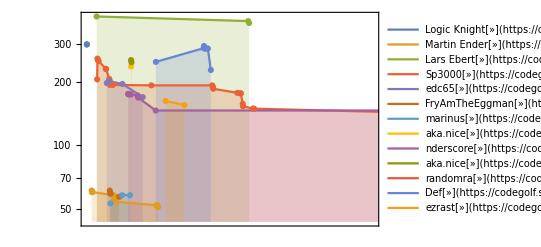

```mathematica
KeyValueMap[
Function[
{post,ts},
Legended[
Tooltip[{#1,QuantityMagnitude[#2["ReportedSize"]]},First[#2["CodeSnippets"],Missing["NotFound"]]]&@@@ts["Path"],
Row[post[{"Owner","SubmissionProgrammingLanguage","URL"}]/.url_URL:>Hyperlink[Style["»",18],url],Spacer[1]]
]
],
submissionToHistoricalCodeGolfMetadata
]//DateListLogPlot[#,Mesh->All,Filling->Axis]&
```

```mathematica
(* TODO: Explore if the rate fits this pretty well over lots of submissions? *)
Size[t_]:=size0+c1+Exp[-k*t]
```

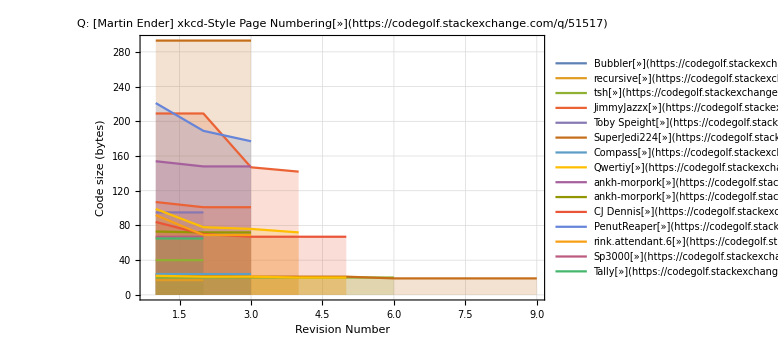

```mathematica
ListPlot[
(#["Values"]&/@DeleteMissing[submissionToSizeHistory])//KeyValueMap[Row[#1[{"Owner","SubmissionProgrammingLanguage","URL"}]/.url_URL:>Hyperlink[Style["»",18],url],Spacer[1]]->QuantityMagnitude[#2]&]//Association//KeySort//Reverse,
PlotRange->Full,
(*PlotLegends->None,*)
ImageSize->Large,
Filling->Axis,
Joined->True,
PlotTheme->"Detailed",
FrameLabel->{"Revision Number","Code size (bytes)"},
PlotLabel->Entity["StackExchange.Codegolf:Post","51517"]
]
```

#### Language URLCounts

```mathematica
EntityProperty["CodeGolfProgrammingLanguage","URLCounts"]["Label"]="URL counts";
EntityProperty["CodeGolfProgrammingLanguage","URLCounts"]["DefaultFunction"]=EntityFramework`BatchApplied[Lookup[languageToURLCounts,#,<||>]&/*Map[KeyMap[URL]]];
Entity["CodeGolfProgrammingLanguage","Rust::8y9w4"]["URLCounts"]
```

<|URL[https://www.rust-lang.org/]→58,URL[https://www.rust-lang.org/en-US/]→2,URL[http://www.rust-lang.org/]→2,URL[https://play.rust-lang.org/?version=stable&mode=debug&edition=2018&gist=309e94d8fe6a66c402a09901e9af5621]→1,URL[https://rust-lang.org]→1,URL[https://play.rust-lang.org/?version=stable&mode=debug&edition=2015&gist=3f493af80510e031bd0c7f85f4cd3497]→1,URL[https://oeis.org/A000141]→1,URL[https://oeis.org/A000001]→1,URL[http://rust-lang.org/]→1|>

#### Language URL

```mathematica
EntityProperty["CodeGolfProgrammingLanguage","URL"]["Label"]="URL";
EntityProperty["CodeGolfProgrammingLanguage","URL"]["DefaultFunction"]=EntityFramework`BatchApplied[
RightComposition[
EntityProperty["CodeGolfProgrammingLanguage","URLCounts"],
Keys,
Map[First[#,Missing["NotAvailable"]]&]
]
];
Entity["CodeGolfProgrammingLanguage","Rust::8y9w4"]["URL"]
```

URL[https://www.rust-lang.org/]

#### User Interpreted Location

```mathematica
userToLocationDescription=DeleteMissing@EntityValue["StackExchange.Codegolf:User","Location","EntityAssociation"];
userToLocationDescription//Length
```

36962

```mathematica
normalizeLocationString=RightComposition[
StringTrim,
StringReplace[
{
d:NumberString~~"°"~~(Whitespace|"")~~m:NumberString~~"'"|"′"~~(Whitespace|"")~~("x"..)~~"\""~~(Whitespace|"")~~dir:("N"|"E"|"S"|"W"):>d<>"° "<>m<>"' "<>dir,
timeZone:("GMT"~~Whitespace~~("+"|"-")~~Whitespace~~DigitCharacter..~~((":"|"."~~DigitCharacter..)|"")):>StringDelete[timeZone,Whitespace]
}
]
];
```

```mathematica
uniqueLocationStrings=userToLocationDescription//RightComposition[
Values,
normalizeLocationString,
Union
];
uniqueLocationStrings//Length
```

8003

```mathematica
$LocationTypes={"City","AdministrativeDivision","Country","University","TimeZone","Location"};
```

```mathematica
locationStringToInterpretedLocation=AssociationThread[#->Interpreter[Alternatives@@$LocationTypes][#]]&[uniqueLocationStrings];//AbsoluteTiming
```

Interpreter::timeout: A network operation for Interpreter timed out. Please try again later.

General::stop: Further output of Interpreter::timeout will be suppressed during this calculation.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

GeoPosition::missloc: Unable to obtain location information for 0.0.0.0.

GeoPosition::missloc: Unable to obtain location information for ::1.

GeoPosition::missloc: Unable to obtain location information for 120.0.0.1.

General::stop: Further output of GeoPosition::missloc will be suppressed during this calculation.

{3995.7,Null}

```mathematica
SetDirectory[NotebookDirectory[]];
Export["locationStringToInterpretedLocation_"<>StringReplace[DateString["ISODateTime"],{"T"->"_",":"->"-"}]<>".mx",locationStringToInterpretedLocation]
```

locationStringToInterpretedLocation_2019-10-22_15-24-04.mx

```mathematica
SetDirectory[NotebookDirectory[]];
locationStringToInterpretedLocation=Import["locationStringToInterpretedLocation_2019-10-22_15-24-04.mx"];
```

```mathematica
locationStringToInterpretedLocation[[;;2]]
```

<|→Missing[NoInput],!→Failure[…]|>

```mathematica
ClearAll[extractLocation];
extractLocation[s_String]:=With[
{
locationsFound=TextCases[s,{"City","Country","AdministrativeDivision","University","TimeZone","Location"}->"Interpretation"]
},
Replace[
FirstCase[Values[KeyDrop[locationsFound,{"Location"}]],_Entity,Missing["NotFound"],Infinity],
{
_Missing:>First[locationsFound["Location"],Missing["NotFound"]]
}
]
];
extractLocation["Al Kharga, Qesm Al Wahat Ad Dakhlah, Egypt"]
```

Egypt

```mathematica
ReverseSort@CountsBy[Values@locationStringToInterpretedLocation,Head]
```

GeoPosition::missloc: Unable to obtain location information for 0.0.0.0.

GeoPosition::missloc: Unable to obtain location information for ::1.

GeoPosition::missloc: Unable to obtain location information for 120.0.0.1.

General::stop: Further output of GeoPosition::missloc will be suppressed during this calculation.

<|Entity→5687,GeoPosition→1562,Failure→747,Missing→7|>

```mathematica
failedLocationStringToExtractedLocation=AssociationMap[extractLocation,Keys[Select[locationStringToInterpretedLocation,MatchQ[_Failure]]]];//AbsoluteTiming
failedLocationStringToExtractedLocation//Length
```

{168.394,Null}

747

```mathematica
ReverseSort@CountsBy[Values@failedLocationStringToExtractedLocation,Head]
```

<|Missing→411,Entity→291,String→39,GeoPosition→6|>

Not really any legit location stuff in English left:

```mathematica
Keys[Select[failedLocationStringToExtractedLocation,MatchQ[_Missing]]]
```

{!,-,.,௵,--,~/,...,娘ターツ,海宁市，中国,-------,想像フォレスト,Ｈｏｇｗａｒｔｓ,ملكوت الله,مصر،القاهرة,日本鹿児島県 奄美大島,德国巴登－符腾堡州卡尔斯鲁厄,(0, 0, 0, 0) relative to myself,0x00000000,0x08048000,0x77CCFA53,0xBF884242,131893000b274c63a71f2bf1f0a623b6,1999法轮功，2018包子露宪,211 63411Arabis saudita,21853155,24 de trieu thi tran cau ngang tra vinh,27kotam thanh pho buon ma thuot tinh daklak Viet Nam,290 Thomas Street, PO Box 234, Dandenong, VIC 3175,74570ST, E9940AVE,942841-space, hacking into your computer.,9830985393,Acidalia Planitia,A galaxy far.... far away,Alapaevsky, Алапаевск, Свердловская область, Россия,a million miles from a second ago,A minor planet of a very average star.,an email away,Ankh-Morpork,An NSA database,Annúminas, Arnor,Another Platform,Anti-matter space,A place on earth,Ask later,a small country you probably never heard of,At an ipython shell near you,At a photoshoot in Heaven,Atashi no yume...,At location (3,4) in a spacious terrarium (an integral distance to the origin),at my forum oliviasrodriguez.nstars.org,At my keyboard,At the corner of the flat Earth.,AxcNscl,Basement (probably),Basement somewhere in Equestria,Beep Boop Maggot,Behind a Keyboard,Behind the keyboard,Behind the rabbit,Behind your TV,Behind you, to the right.,中国北京市Beijing,中国北京市Beijing Shi,between bits & bytes,Bharatavarsha,Binarnia,Binary Void,BirkenVegas,Camorr,Caves beneath Helms Deep,Center Europe,Central Europe,CEO & Founder,Chatgoat's Barn,China上海市Shanghai,ChinaZhejiangHangzhou,Civilization Type V,click "say-hello" in about me,Code desert,Coffee Shops and my bed,Cupertino, 加利福尼亚州美国,Darkest Andalucia,Deathstar,declarative world,Deep space, on the rim of...,DeleteMe,Depends,derpyville,/dev/kmem,/dev/null,/dev/sda1,/dev/urandom,Did you know that Opinion Outpost offers paid online surveys in 7 different countries around the wor,Distributed / Decentralized,Does not matter,do you really need to know?,drifting with you somewhere on our BelovedBeautiful BlueBoulder bounding through infinite SpaceTime,dsfsd,Dune Sea, Tatooine,,Earth, Alpha Centauri,Earth, C-137 Rick,Earth (currently),Earth...I think,Earth I Think,earth:localhost,Earth, Local Interstellar Cloud, Gould Belt, Orion Arm, Virgo Supercluster, Universe,Earth, Milky Way Galaxy,Earth, Milkyway Galaxy,Earth, Mostly,Earth.Prefer Moving to Mars when Musk has his mission accomplished, of course before I die. ;),Earth, Solar system,Earth, Solar system.,Earth, Star system Sol, Galctic sector ZZ9 Plural Z Alpha,Earth, The Solar System, Milky Way, Universe,Earth (weekdays), Mars (weekends),Earth, Western Hemisphere, above the equator,easy come, easy go,Enter a location,Enter a Location,Europe, GMT+1,Europe, somewhere,Everywhere and Nowhere,Exists and is unique,(e^π - π) metres west of previously observed location,Factory 1, 3 Oban Road, Ringwood VIC 3134,Far away from you…,Farewell Stack Exchange,Flo Ridaa.,Forgotten Realms,From the River to the Sea,Galactic sector ZZ9 Plural Z Alpha,Ganymede, Jupiter,Glory to Arstotzka!,GMT -8:00,中国广东省Guangzhou Shi,Hangin' with the Funky Bunch,中国浙江省Hangzhou Shi,Headquarter of 043,中国安徽省Hefei,中国安徽省Hefei Shi,He's in your house!,Hey bubs "Phonesaber Unlock" Google Play Store free no ads!,hhhh - Condomínio Império dos Nobres, Bra-xi-li-a - Quận Liên bang, Bra-xin,Hilbert Space,/home/bedroom/bed,/home/motte001,Hopefully at home,Hyrule,I live where the sky ends,Imagine, it can be what you want it to be.,I'm not telling you my location; I thought we were playing hide and seek!,In a cave somewhere,In a galaxy far far away..,In a pasture with other giant cows,In close proximity to bacon,in front of a computer :3,In front of a screen,in front of my computer,In front of my computer,In front of the computer,In my own world,Inside my meticulously constructed mental Library,Inside the intertubes!,Inside your computer,Institute for Disease Modeling,Internet Cloud,Interstellar Transport Station #854,Interweb,Interwebs,In the Dark Realm,in the matrix ( not really ),In the middle of town,In the nullspace of a non-singular matrix,In the puɐlǝʇsɐM,In the shadows behind you...,In the VOID of the web.,in this world at in this universe,In your code,In your computer ( ͡° ͜ʖ ͡°),In your imagination,Island of misfit toys,javascript,jjwaw,com,JO22,junior developer,Just before the ROM, after the RAM, with an ARM,Just North of the world longest border,JVM eden space,Known Universe,Laboratorios Prady-Normapiel SL Pol. Ind. Los Torraos C / Asturias, 15 / Aptdo. 96 30562 Ceutí. Mur,Laniakea Supercluster,La Parra, Avila,Legion of Doom Headquarters,Living with a fox,Lobus frontalis,loking 4 u,Magrathea, The Universe,Maria Saal, Österreich,MarioWii:World1,Middle Eart,Middle Earth,Middle TN,Milky Way Galaxy,Minecraft Server: redstoner.com,Mirrodin,Monochromes and then again...,Moon, Sol, Universe,Moschato, Νότιος Τομέας Αθηνών, Ελλάδα,Mountain Standard Tribe,Mulgoure,Must be Inside an NSA Database,my computer, where else?,My map says I am here...,My nama jeff,日本愛知県Nagoya-shi,Namex Planet,中国江西省Nanchang Shi,中国江苏省Nanjing Shi,NDP\mscorelib,near 48.1/16.2,Near Apple HQ,nearest node,Near mountians,Near the Edge of the World..!,Nekede, Nigria.,Neverever,Newarre, The Commonwealth,new Human().setIdentifier("Sahib").getLocation().toString();,Next to a coffee maker.,None of your business,NoOneIsHere's Computer,Northern Hemisphere,Northern Hemisphere, Mars,Not Behind You,Not Happening,NotHereOrThere,Nothomeland,Not in My Backyard,Nowhere, because I don't exist...,Nowhere in Particular,Nowhere in particular...,Nowhere neraby!,Nowhere on this site,Nowhere to be found,Nunya Bidness,observable universe,Occitany,Omicron Persei-8,Omicron Theta,Omnipresent,Online~Home,on the internet wires, looking at the flow of data,On the other side of the mobius strip...,on the server farm,Orion Arm / Milky Way,Orion Arm, Milky Way,Orvwvat, Puvan,@OutskirtsLabs,Over His Throne,P9G5+9F, 35899,pale blue dot,Pale Blue Dot,Pandæmonium, Inférnum,Pencilveinea,Pennsyltucky,Personal Reality,Planet Earth, Milky Way, Observable Universe,Planet Vegeta,Priffdinas, Gielinor,Pringles Factory in the middle of Nowhere,Probably not that infinite plane of uniform density you physicists go on about.,Project Shrine Maiden,Randland,Rathror Estate, Lucaria,Ratio, Logic,Realm 266,Realm of Existence,Remote, Global,Remote (worldwide),Rigel VII,Right Behind You,Ruthless Viking Territory 63°25'50.50 North,Sancta Sedes,sandwiched in your smelly armpit,Saturn, Telesto,sdfgsdf,Sector ZZ 9 Plural Z Alpha,Sector ZZ9 Plural Z Alpha,Sector ZZ Plural Z Alpha,Segmentation Fault,Series of tubes.,中国上海市Shanghai Shi,中国Shanghai Shi上海市,中国广东省Shenzhen Shi,Shop 3 / 477 Dorset Road, Bayswater, Victoria 3153,Silicon Valley, Sol III,Sinny, Straya,Sitting down and facing forward,Some place humans have never been.,Some Place Over The Rainbow,Somewhere around /dev/sda,Somewhere at Universe,somewhere before the alps,Somewhere between 60N-28N and 77W-36E,Somewhere between 6 and Graham's Number,Somewhere between earth and andromeda.,Some where between this world and the other,Somewhere but not here,somewhere far away,Somewhere in Earth!,Somewhere in spacetime,Somewhere in the deep reaches of the Drift,somewhere in the multiverse,Somewhere in the Vast, Ever-Expanding Universe,Somewhere in the void...,Somewhere in the world,Somewhere in the world like IRAN,Somewhere in this World,Somewhere in this world???,Somewhere near the inner rim of the Orion Arm,Somewhere on earth,Somewhere on planet Earth,Somewhere on the left side of the Universe,somewhere on the planet Earth,somewhere over the rainbow,Somewhere over the rainbow,Somewhere over the rainbow...,Somewhere over the rainbows,Southampton / Southend,Spb/Bryansk,sqrt(-1),standing next to carmen sandiego,İstiklal mahallesi 14 nolu sokak no 25 Şahinbey Gaziantep,Stuart's Muscles,Sunny ol' England,surat,gujrat,Sydneattle,System.Exception,TacWa,Tauremornalómë,Terlia,That huge palace built with taxpayer money,theBatCave,The forgotten corner of notevendoommusic.com,The Great Southern Land,the internet (all cardinal directions),The Kat's Kradle,The Middle of Nowhere, The Center of Everywhere,The ministry of silly walks,the neverending void,The Nineteenth Byte,The Observable Universe,The outernet,The Outskirts of the Third World,The planet Xorb,There is no place like 127.0.0.1,The Restaurant at the End of the Universe,The Shattered Plains, Roshar,The Underdark,This I can only guarantee - somewhere I'm not supposed to be.,Tim Booked Two,日本Tōkyō-to,Top of a stack frame,TRAPPIST-1d,Trenzalore,Ukrajyna, Kyjiv,Unallocated disk space,Under a roof, in a place.,Underhat,under the roof of the Sky,under the rug,UnicycleLand,Unitd Stuts of Murka,United States - Pacific Time Zone,Unova,User: 559085,Userland,/usr/bin/python,/usr/dcat,USS Enterprise with my crew.,Utopian Dystopia,u wish u knew,Virgo SuperCluster,virtual memory,waterbird district,Web / Apps Developer,We don't recognize that location -- try again?,Well, if there's a bright center to the universe, [I'm] on the planet that it's farthest from.,Whatever's at the top of the stack when you ret,Where am I? What is this?,Where the cold things are...,where the cookie crumbles,Where the shadows lie,Wherever you live,Wilderness Safaris Rivonia,window.smileycreations15,Wouldn't you like to know...,中国陕西省Xian Shi,中国江苏省Yangzhou Shi,you.getLocation() - 1,Your favorite IDE,Your tilted Gulfstream G650,ýrÐ/ ó, sol±syñem,中国Yunnan Sheng,yurop[sic],Yurp,中国浙江省宁波市Yuyao Shi,中国Zhejiang Sheng,ℂ,,Αθήνα, Κεντρικός Τομέας Αθηνών, Ελλάδα,$$F^{A^{R^{R^{R^{R^{A^{W^{A^{Y}}}}}}}}}$$}

```mathematica
Select[failedLocationStringToExtractedLocation,MatchQ[_String]]
```

<|15303 Ventura Blvd, #900 Sherman Oaks, CA 91403→Sherman Oaks,A Crater on the Moon→Crater,Angband, Beleriand→Beleriand,Any Beach, California→Any Beach, California,Atlantic Rain Forest→Atlantic Rain Forest,Belmont christain college→christain college,Bossland, Boss County, Boss→Boss County,Burbury, Connecticut→Burbury, Connecticut,Clavius Base→Clavius Base,Crown Casino, Shop 17, 8 Whiteman Street, Southbank, VIC 3006→Crown Casino,DC Metro Area→Metro Area,Deep South USA→South,Duchy of Grand Fenwick→Duchy,Earth, Milky Way Galaxy (western spiral), Laniakea Supercluster→Supercluster,Earth, Solar System→System,Earth Wide Web→Wide,EET/EEST→EEST,Free and Democratic China→Democratic China,Gildas Avenue 27 , Birmingham, Suisse→Avenue,HALP IM STUCK IN DOWNGAOTS CLOSET→IM STUCK,Hanoi University of Science, Vietnam National University (HUS-VNU)→Hanoi University of Science, Vietnam National University,HoneyLand. A city in East Coast→East Coast,Iași, Județul Iași, România→Iași,In the Magical Computer World→Magical,in the middle of, but not in the EU→EU,ISD Chimera→ISD,Nahsville, TN→Nahsville, TN,Nibelheim→Nibelheim,SF Bay Area, CA→SF Bay Area,SF/NOLA→NOLA,Silicon Valley Bangalore, KA,→Silicon Valley Bangalore, KA,The Cabin on the Mystery Island→Mystery Island,The Glorious California Bay Area→California Bay,The Kingdom of Arendelle→Kingdom of Arendelle,The Mars，Solis Lacus→Lacus,The Valley of Saints, Kashmir.→Kashmir,Town of Socks→Socks,Universe, Milky Way, Solar System, Planet Earth.→System,U.S. East Coast→U|>

```mathematica
locationStringToInterpretedLocationFinal=Join[
Select[locationStringToInterpretedLocation,MatchQ[_Entity|_GeoPosition]],
Select[failedLocationStringToExtractedLocation,MatchQ[_Entity|_GeoPosition]]
];
locationStringToInterpretedLocationFinal//Length
```

7546

```mathematica
ReverseSort@CountsBy[Values[locationStringToInterpretedLocationFinal],Head]
```

<|Entity→5978,GeoPosition→1568|>

```mathematica
locationStringToInterpretedLocationFinal[[;;10]]
```

<|中国→China,北京→GeoPosition[{39.906,116.391}],日本→Japan,東京→Tokyo,神戸→Kobe,Киев→GeoPosition[{50.4501,30.5241}],Крым→GeoPosition[{45.2835,34.2008}],Минск→GeoPosition[{53.9023,27.5619}],Чехия→GeoPosition[{49.8167,15.475}],中国北京市→GeoPosition[{39.906,116.391}]|>

Align to users now as a property:

```mathematica
EntityProperty["StackExchange.Codegolf:User","InterpretedLocation"]["Label"]="interpreted location";
KeyValueMap[(#1["InterpretedLocation"]=#2;)&,userToLocationDescription];//AbsoluteTiming
```

{5.65957,Null}

Gradually convert towards continents:

```mathematica
nearestContinent=AssociationMap[
RightComposition[
EntityList,
EntityProperty["Country","Position"],
DeleteMissing[#][[All,1]]&
],
{EntityClass["Country","NorthAmerica"],EntityClass["Country","Europe"],EntityClass["Country","Asia"],EntityClass["Country","SouthAmerica"],EntityClass["Country","Africa"],EntityClass["Country","Oceania"],EntityClass["Country","Antarctica"]}
]//KeyValueMap[Thread[Rule[#2,#1]]&]//Flatten//Nearest
```

NearestFunction[…]

```mathematica
interpretedLocationContinents=Fold[
Function[
{entities,patternToFunction},
SubsetMap[Last@patternToFunction,entities,Position[entities,First@patternToFunction]]
],
Values[locationStringToInterpretedLocationFinal],
{
Entity["AdministrativeDivision"|"City"|"University",___]->(EntityValue[#,"Country"]&),
Entity["TimeZone",___]->(EntityValue[#,"Countries"]&/*Map[First]),
Entity["Country",___]->(EntityValue[#,"Continent"]&),
GeoPosition[{_?NumericQ,_?NumericQ}]->(#[[All,1]]&/*nearestContinent/*Map[Replace[{{x_,___}:>x,{}->Missing["NotFound"]}]]),
GeoPosition[_Entity]->(ConstantArray[Missing["NotAvailable"],Length[#]]&)
}
];
locationStringToContinent=AssociationThread[Keys[locationStringToInterpretedLocationFinal]->interpretedLocationContinents];
```

```mathematica
continentToCount=Values[locationStringToContinent]//Counts//ReverseSort
```

<|North America→3079,Europe→2275,Asia→1411,South America→333,Oceania→202,Africa→199,Missing[NotAvailable]→45,Antarctica→2|>

```mathematica
GeoRegionValuePlot[continentToCount]
```

-Graphics-

```mathematica
EntityProperty["StackExchange.Codegolf:User","Continent"]["Label"]="continent";
KeyValueMap[
(
#1["Continent"]=.;
#1["Continent"]=Lookup[locationStringToContinent,normalizeLocationString[#2],Missing["NotAvailable"]];
)&,
DeleteMissing[userToLocationDescription]
];//AbsoluteTiming
```

{14.1268,Null}

## Export cleaned up EntityStores

Export these cleaned up EntityStores for further exploration in Explore.nb:

```mathematica
SetDirectory[NotebookDirectory[]];
Export["codegolf.stackexchange.com_Cleaned_"<>StringReplace[DateString["ISODateTime"],{":"->"-","T"->"_"}]<>".mx",Entity["StackExchange.Codegolf:Post"]["EntityStore"]]
```

codegolf.stackexchange.com_Cleaned_2019-10-23_11-29-19.mx

```mathematica
SetDirectory[NotebookDirectory[]];
Export["CodeGolfProgrammingLanguage_Cleaned_"<>StringReplace[DateString["ISODateTime"],{":"->"-","T"->"_"}]<>".mx",Entity["CodeGolfProgrammingLanguage"]["EntityStore"]]
```

CodeGolfProgrammingLanguage_Cleaned_2019-10-23_11-29-57.mx

## Upload EntityStores to the Wolfram Cloud

### Compress for easier sharing

```mathematica
SetDirectory[NotebookDirectory[]];
CreateArchive["codegolf.stackexchange.com_Cleaned_2019-10-23_11-29-19.mx"]
CreateArchive["CodeGolfProgrammingLanguage_Cleaned_2019-10-23_11-29-57.mx"]
```

### Upload to Wolfram Cloud

```mathematica
SetDirectory[NotebookDirectory[]];
CopyFile[
"codegolf.stackexchange.com_Cleaned_2019-10-23_11-29-19.mx.zip",CloudObject["StackExchange2EntityStore/codegolf.stackexchange.com_Cleaned.mx.zip",Permissions->"Public"],
OverwriteTarget->True
]
CopyFile[
"CodeGolfProgrammingLanguage_Cleaned_2019-10-23_11-29-57.mx.zip",CloudObject["StackExchange2EntityStore/CodeGolfProgrammingLanguage_Cleaned.mx.zip",Permissions->"Public"],
OverwriteTarget->True
]
```

CloudObject[https://www.wolframcloud.com/obj/andrews/StackExchange2EntityStore/codegolf.stackexchange.com_Cleaned.mx.zip]

CloudObject[https://www.wolframcloud.com/obj/andrews/StackExchange2EntityStore/CodeGolfProgrammingLanguage_Cleaned.mx.zip]